# HRI and the SFS

## Parameters

## Formulae

### Get Ne

```mathematica
U=L u
```

L u

```mathematica
Vm=U s^2
```

L s^2 u

```mathematica
γ0=2NN s
```

2 NN s

```mathematica
α0=2NN U
```

2 L NN u

```mathematica
γ=2B γ0
```

4 B NN s

Gamma0 here too?

```mathematica
Vg=(U s(1-Exp[-γ0]))/(1+κ Exp[-γ0])
```

((1-ⅇ^(-2 NN s)) L s u)/(1+ⅇ^(-2 NN s) κ)

Eq 3

```mathematica
eq3=(Vg^3/Vm^2/.NN->(B NN))+Log[B]
```

((1-ⅇ^(-2 B NN s))^3 L u)/(s (1+ⅇ^(-2 B NN s) κ)^3)+Log[B]

```mathematica
getPbar[kk_,ss_,NN_]:=1/(1+kk Exp[-2NN ss])
```

```mathematica
getGammaHat[kk_,pBar_]:=Log[(kk pBar)/(1-pBar)]
```

Expected p bar

```mathematica
getPbar[1,10^-4,1000]//N
```

0.549834

```mathematica
getGammaHat[1,#]&/@{0.529,0.533,0.537}
```

{0.11613,0.132192,0.148271}

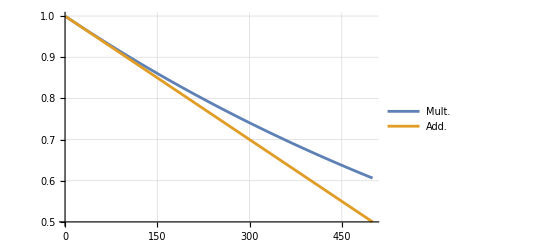

```mathematica
Plot[{(.999)^x,1-(1-0.999)x},{x,1,500},GridLines->Automatic,PlotLegends->{"Mult.", "Add."}]
```

```mathematica
getGammaHat[1,1-Log[0.955]/Log[0.9999]/1000]
```

0.158667

```mathematica
getGammaHat[1,0.536]
```

0.14425

```mathematica
0.9999^550
```

0.946483

```mathematica
params1={NN->1000,s->10^-4,κ->1,L->2500,u->10^-5}
```

{NN→1000,s→1/10000,κ→1,L→2500,u→1/100000}

```mathematica
params2={NN->1000,s->10^-3,κ->1,L->10000,u->10^-5}
```

{NN→1000,s→1/1000,κ→1,L→10000,u→1/100000}

```mathematica
eq302=eq3/.params2
```

(100 (1-ⅇ^(-2 B))^3)/((1+ⅇ^(-2 B))^3)+Log[B]

```mathematica
bfun02[a_]:=eq302/.B->a
```

```mathematica
bfun02[.2]
```

-0.840523

```mathematica
Clear[newtonRoot]
```

```mathematica
newtonRoot[fun:_Symbol|_Function, init_Real, tol_:1.*^-100]:=
Module[{funp},funp=Derivative[1][fun];
NestWhile[#-fun[#]/funp[#]&,init,Abs[Subtract[##]]>=tol&,2]
]
```

May need to adjust starting value (2nd argument) if this fails:

```mathematica
bsel02=newtonRoot[bfun02[#]&,0.1]
```

0.245999

```mathematica
pbarExp02=getPbar[1,10^-3,1000 bsel02]
```

0.620577

### Get Ne trajectory for neutral sites

```mathematica
Qt=(Vg/Vm (1-1(1-Vm/Vg)^(τ+1)))
```

((1-ⅇ^(-2 NN s)) (1-(1-(s (1+ⅇ^(-2 NN s) κ))/(1-ⅇ^(-2 NN s)))^(1+τ)))/(s (1+ⅇ^(-2 NN s) κ))

```mathematica
params2
```

{NN→1000,s→1/1000,κ→1,L→10000,u→1/100000}

```mathematica
Nprime[B_,params_]:=
NN/Exp[(Vg /.NN->(NN B)) (Qt/.NN->(NN B))^2]/.params
```

```mathematica
np02=Nprime[bsel02,params2]
```

1000 ⅇ^(-1.40243 (1-0.995853^(1+τ))^2)

```mathematica
np02/.τ->#&/@{0, 500,1000,1500,2000}
```

{999.976,341.479,256.924,247.35,246.168}

#### Ne plots

```mathematica
Nprime01=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-8//Simplify
```

10000 ⅇ^(-192/1811-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/(10 (1+1/(10 ⅇ^2))^3))

```mathematica
Nprime02=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-7//Simplify
```

10000 ⅇ^(-19200/49331-((-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Nprime03=Nprime/.NN->10000/.s->10^-4/.κ->1/10/.L->1000/.u->10^-6//Simplify
```

10000 ⅇ^(-1920000/4801331-(10 (-1+(1-(1+1/(10 ⅇ^2))/(10000 (1-1/ⅇ^2)))^(1+τ))^2 (1-1/ⅇ^2)^3)/((1+1/(10 ⅇ^2))^3))

```mathematica
Plot[{Nprime01/.τ->x,Nprime02/.τ->x,Nprime03/.τ->x},{x,0,100000}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8","u=10^-7","u=10^-6"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

```mathematica
Plot[{NprimeSc01/.τ->x},{x,0,10}, PlotRange->{Automatic,{0, 10000}},GridLines->Automatic,PlotLabels->{"u=10^-8"},AxesLabel->{"τ (Generations)", "Ne"},ImageSize->Large]
```

-Graphics-

#### Expressions from Polanski and Kimmel. 2003

The calculations below follow the approach of Polanski, A., and Kimmel, M. (2003). New Explicit Expressions for Relative Frequencies of Single-Nucleotide Polymorphisms With Application to Statistical Inference on Population Growth.” Genetics 165:427–436. The equation numbers used by Polanski and Kimmel (2003) are indicated here and in the exponential growth section.

Equation 6 (coefficient used in equations 9 and 10):

```mathematica
Akjn[k_,j_,n_]:=Product[Binomial[l,2],{l,Select[Range[k,n],#≠j&]}]/Product[Binomial[l,2]-Binomial[j,2],{l,Select[Range[k,n],#≠j&]}]
```

Equation 9 (coefficient used in equation 8):

```mathematica
vnj[n_,j_]:=Sum[j(j-1)Akjn[k,j,n]/(k-1),{k,2,j}]
```

Equation 10 (coefficient used in equation 8):

```mathematica
wnbj[n_,b_,j_]:=Sum[j(j-1)Binomial[n-k,b-1]((n-b-1)!(b-1)!)/((n-1)!)Akjn[k,j,n],{k,2,j}]
```

### Doing it on HRI

#### Piecewise approx

*Get extrema from Brian’s message
* get inverse with respect to τ
* make τ intervals so that the Δy are equal

```mathematica
kk=1
```

1

```mathematica
nPrimeAndLimits[ee_]:=
{ee, ee/.τ->0,ee/.τ->∞}
```

Should s be pos or neg? Either give reasonable trajectories.

```mathematica
rAndL=nPrimeAndLimits[np02];
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.40243 (1-0.995853^(1+τ))^2),999.976,245.999}

```mathematica
{x->#,y->rAndL⟦1⟧/.τ->#}&/@Range[0,5000,500]//N
```

{{x→0.,y→999.976},{x→500.,y→341.479},{x→1000.,y→256.924},{x→1500.,y→247.35},{x→2000.,y→246.168},{x→2500.,y→246.02},{x→3000.,y→246.001},{x→3500.,y→245.999},{x→4000.,y→245.999},{x→4500.,y→245.999},{x→5000.,y→245.999}}

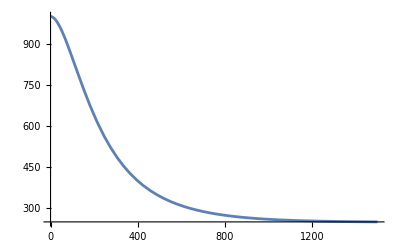

```mathematica
Plot[rAndL⟦1⟧,{τ,0,1500}]
```

```mathematica
getInv[ral_]:=Solve[{ral⟦1⟧==y},τ]
```

```mathematica
rAndL
```

{1000 ⅇ^(-1.40243 (1-0.995853^(1+τ))^2),999.976,245.999}

```mathematica
inv=getInv[rAndL];
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
inv/.y->660//N
```

{{τ→188.144},{τ→-105.584}}

```mathematica
inv
```

{{τ→-240.653 Log[2.03884×10^-16 (4.92518×10^15-1. √(2.42574×10^31-1.72967×10^31 Log[0.00406506462806175 y]))]},{τ→-240.653 Log[2.0388377414925×10^-16 (4.9251786044741×10^15+√(2.425738428597×10^31-1.7296685386234×10^31 Log[0.00406506462806175 y]))]}}

```mathematica
inv2=inv⟦1,1,2⟧
```

-240.653 Log[2.03884×10^-16 (4.92518×10^15-1. √(2.42574×10^31-1.72967×10^31 Log[0.00406506462806175 y]))]

```mathematica
inv2/.y->660//N
```

188.144

#### Breaks, even x steps

```mathematica
getXs[ral_,n_,inv_]:=Module[{fiveP=(ral⟦2⟧-ral⟦3⟧)/20+ral⟦3⟧},
Subdivide[0,inv/.y->fiveP,n]
]
```

```mathematica
xs=getXs[rAndL,10,inv2];
```

```mathematica
xs//N
```

{0.,70.9587,141.917,212.876,283.835,354.793,425.752,496.711,567.67,638.628,709.587}

```mathematica
{1,2,3,4,5}+1/2
```

{3/2,5/2,7/2,9/2,11/2}

```mathematica
getYs[xs_,ral_]:=Module[{dd=xs⟦2⟧-xs⟦1⟧},
Join[{ral⟦2⟧},ral⟦1⟧/.τ->#&/@((xs//Rest//Most)+dd/2),{ral⟦3⟧}]
]
```

```mathematica
ys=getYs[xs,rAndL];
```

```mathematica
ys//N
```

{999.976,833.721,680.894,557.785,468.012,404.587,360.011,328.525,306.101,289.992,245.999}

```mathematica
xy1={xs,ys}//N
```

{{0.,70.9587,141.917,212.876,283.835,354.793,425.752,496.711,567.67,638.628,709.587},{999.976,833.721,680.894,557.785,468.012,404.587,360.011,328.525,306.101,289.992,245.999}}

#### Breaks, even y steps

```mathematica
getEquiDistYs[ral_,n_,inv_]:=Module[{
ys=Join[{ral⟦2⟧},ral⟦2⟧-Range[1,n-1](ral⟦2⟧-ral⟦3⟧)/n,{ral⟦3⟧}]},
{Join[{0},inv/.y->#&/@(Most[ys]-((ral⟦2⟧-ral⟦3⟧)/n/2))],ys}
]
```

```mathematica
xy2=getEquiDistYs[rAndL,10,inv2]//N
```

{{0.,42.5644,82.295,116.358,150.619,187.785,230.6,283.207,353.689,462.985,709.587},{999.976,924.578,849.18,773.783,698.385,622.987,547.589,472.192,396.794,321.396,245.999}}

#### Return to function

```mathematica
Nprime01p=D[rAndL⟦1⟧,τ]
```

-11.6552 0.995853^(1+τ) (1-0.995853^(1+τ)) ⅇ^(-1.40243 (1-0.995853^(1+τ))^2)

```mathematica
Nprime01p/.τ->-10//N
```

4.70838

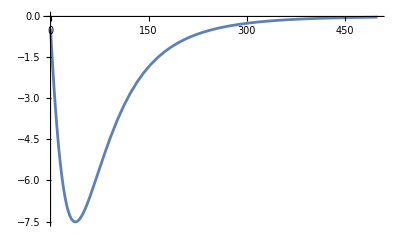

```mathematica
Plot[Nprime01p/.τ->t,{t,0,500}]
```

Assuming Nprime is monotonously decreasing, take values as x=0 and limit for x→∞

```mathematica
makePiecewiseTraj[xys_]:=Module[{pRules0={n,x<a}/.a->#1/.n->#2&@@@Transpose[{Rest[xys⟦1⟧],Most[xys⟦2⟧]}]},
Piecewise[Join[pRules0,{{Last[xys⟦2⟧],x>Last[xys⟦1⟧]}},{{0,True}}]//N]]
```

```mathematica
pwNe1=makePiecewiseTraj[xy1]
```

Piecewise[{{999.976, x<70.9587}, {833.721, x<141.917}, {680.894, x<212.876}, {557.785, x<283.835}, {468.012, x<354.793}, {404.587, x<425.752}, {360.011, x<496.711}, {328.525, x<567.67}, {306.101, x<638.628}, {289.992, x<709.587}, {245.999, x>709.587}, {0., True}}]

```mathematica
pwNe2=makePiecewiseTraj[xy2]
```

Piecewise[{{999.976, x<42.5644}, {924.578, x<82.295}, {849.18, x<116.358}, {773.783, x<150.619}, {698.385, x<187.785}, {622.987, x<230.6}, {547.589, x<283.207}, {472.192, x<353.689}, {396.794, x<462.985}, {321.396, x<709.587}, {245.999, x>709.587}, {0., True}}]

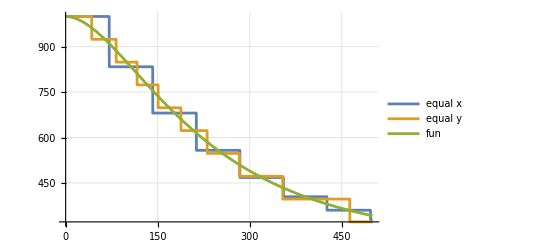

```mathematica
Plot[{pwNe1/.x->t,pwNe2/.x->t,rAndL⟦1⟧/.τ->t},{t,0,500},GridLines->Automatic,ImageSize->400,PlotLegends->{"equal x","equal y","fun"}]
```

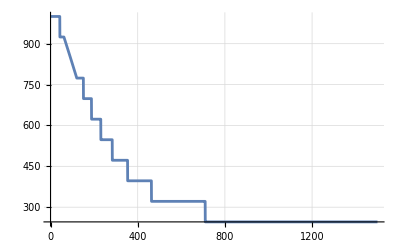

```mathematica
Plot[pwNe2/.x->t,{t,0,1500},GridLines->Automatic,ImageSize->400]
```

```mathematica
pwNe=pwNe2
```

Piecewise[{{999.976, x<42.5644}, {924.578, x<82.295}, {849.18, x<116.358}, {773.783, x<150.619}, {698.385, x<187.785}, {622.987, x<230.6}, {547.589, x<283.207}, {472.192, x<353.689}, {396.794, x<462.985}, {321.396, x<709.587}, {245.999, x>709.587}, {0., True}}]

```mathematica
pwNe/.x->1000//N
```

245.999

```mathematica
qjtHriPw01[j_]:=Binomial[j,2]/pwNe Exp[-Integrate[Binomial[j,2]/(pwNe/.x->σ),{σ,0,x},Assumptions->x∈]]
```

Prob of coalescence for a pair of lineages at given time:

```mathematica
qjtHriPw01[2]/.x-> 600//N//AbsoluteTiming
```

{0.936671,0.00090133}

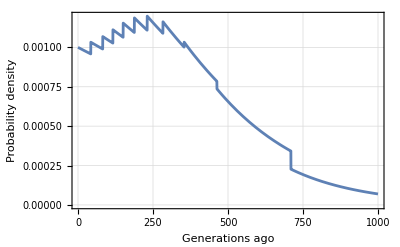

```mathematica
Plot[qjtHriPw01[2],{x,0,1000},Frame->True,FrameLabel->{"Generations ago","Probability density"},GridLines->Automatic]
```

Equation 3 (the expectation of equation 4):

```mathematica
ejHriPw[j_]:=Integrate[x qjtHriPw01[j],{x,0,∞}, Assumptions->x∈Reals]
```

Expected coalescence time for a pair of lineages.

2 steps 1.4s, 2 steps 3.2s, 4 steps 13s, 5 steps 62s

Is is much faster to use Integrate[] with Assumptions→x∈Reals than PiecewiseIntegrate[]:
5steps 10s, 8steps 18s,9 steps 21s

```mathematica
a01=(ejHriPw[2]//AbsoluteTiming)
```

{11.3412,467.565}

```mathematica
a01[[2]]
```

467.565

Equation 8 (an expression for the probability to see b derived alleles in a sample of n):

```mathematica
qnbHriPw[n_,b_]:=Sum[ejHriPw[j]wnbj[n,b,j],{j,2,n}]/Sum[ejHriPw[j]vnj[n,j],{j,2,n}]
```

```mathematica
n10All=AbsoluteTiming[n10b1=qnbHriPw[10,#]]&/@Range[1,9]
```

{{154.296,0.471809},{126.107,0.184262},{124.834,0.103775},{124.183,0.0689793},{123.568,0.0504478},{123.287,0.0392473},{122.402,0.0318711},{121.932,0.0267023},{121.591,0.022906}}

```mathematica
Export["v04sfs10.txt", n10All]
```

v04sfs10.txt

```mathematica
n20All=AbsoluteTiming[n20b1=qnbHriPw[20,#]]&/@Range[1,19]
```

{{303.957,0.397395},{269.726,0.165371},{269.026,0.0959434},{268.681,0.0645213},{268.404,0.047268},{269.884,0.0366353},{269.654,0.0295527},{268.609,0.0245612},{267.965,0.020889},{267.589,0.0180944},{267.766,0.0159085},{267.56,0.0141596},{267.466,0.0127334},{267.33,0.0115513},{267.008,0.0105579},{267.081,0.00971278},{266.758,0.00898612},{266.58,0.00835543},{266.612,0.00780342}}

```mathematica
Export["v04sfs20.txt", n20All]
```

v04sfs20.txt

```mathematica
n40All=AbsoluteTiming[n40b1=qnbHriPw[40,#]]&/@Range[1,39]
```

{{634.466,0.339385},{566.778,0.149706},{565.882,0.0900601},{566.231,0.0619677},{566.223,0.046051},{566.238,0.035995},{566.555,0.0291634},{566.269,0.0242737},{566.457,0.020633},{566.936,0.0178371},{567.309,0.0156354},{567.094,0.0138654},{567.238,0.0124173},{567.475,0.0112149},{567.513,0.0102034},{567.305,0.0093429},{567.396,0.00860356},{567.203,0.00796267},{566.989,0.00740271},{566.998,0.00690998},{566.884,0.0064736},{566.954,0.00608486},{566.908,0.00573671},{566.761,0.00542339},{566.825,0.00514013},{566.862,0.00488298},{566.989,0.00464865},{566.369,0.00443435},{566.413,0.0042377},{566.292,0.00405671},{566.19,0.00388963},{566.303,0.00373499},{566.446,0.00359149},{566.484,0.00345802},{565.993,0.00333358},{565.716,0.00321733},{565.826,0.00310851},{566.445,0.00300645},{566.399,0.00291055}}

```mathematica
Export["v04sfs40.txt", n40All]
```

v04sfs40.txt

```mathematica
n80All=AbsoluteTiming[n80b1=qnbHriPw[80,#]]&/@Range[1,79]
```

{{1344.58,0.291508},{1223.13,0.134701},{1218.81,0.0838089},{1216.78,0.0591302},{1218.87,0.0447885},{1219.05,0.0355277},{1227.4,0.029116},{1217.46,0.0244501},{1217.15,0.0209251},{1216.37,0.0181828},{1216.3,0.0159986},{1216.09,0.0142249},{1216.48,0.012761},{1216.6,0.0115359},{1216.67,0.0104985},{1217.07,0.00961081},{1216.62,0.00884426},{1216.77,0.00817693},{1215.43,0.00759173},{1214.77,0.0070752},{1215.17,0.00661657},{1214.83,0.00620715},{1214.63,0.00583985},{1214.82,0.00550885},{1214.13,0.00520931},{1214.41,0.0049372},{1214.36,0.00468912},{1214.43,0.0044622},{1216.77,0.00425398},{1215.47,0.00406237},{1214.62,0.00388557},{1214.63,0.00372201},{1214.51,0.00357034},{1214.42,0.00342938},{1214.33,0.00329809},{1214.32,0.00317555},{1214.31,0.00306098},{1214.29,0.00295365},{1215.8,0.00285294},{1217.38,0.00275827},{1216.5,0.00266916},{1214.94,0.00258514},{1214.64,0.00250582},{1214.79,0.00243083},{1214.61,0.00235984},{1214.7,0.00229256},{1217.15,0.00222871},{1217.22,0.00216806},{1216.65,0.00211037},{1216.68,0.00205545},{1220.32,0.00200311},{1216.65,0.00195318},{1216.1,0.00190551},{1216.23,0.00185994},{1215.94,0.00181636},{1216.37,0.00177464},{1216.93,0.00173466},{1217.07,0.00169633},{1217.26,0.00165955},{1217.38,0.00162423},{1216.87,0.00159029},{1216.88,0.00155766},{1216.94,0.00152625},{1216.56,0.00149601},{1216.18,0.00146688},{1216.62,0.00143879},{1216.88,0.0014117},{1216.67,0.00138555},{1215.72,0.0013603},{1215.5,0.0013359},{1214.91,0.00131231},{1215.42,0.0012895},{1215.42,0.00126743},{1215.24,0.00124606},{1215.22,0.00122536},{1214.81,0.0012053},{1215.33,0.00118586},{1214.82,0.001167},{1217.95,0.0011487}}

```mathematica
Export["v04sfs80.txt", n80All]
```

v04sfs80.txt

```mathematica
sfs01=#⟦2⟧&/@n12All
```

{0.413224,0.177479,0.105818,0.0728697,0.0545042,0.0430248,0.035276,0.0297467,0.0256311,0.0224646,0.0199623}

```mathematica
#⟦2⟧&/@n12All//Total
```

1.

Expected π is ejHriPw[2] × 2 × μ

```mathematica
a01⟦2⟧
```

599.115

```mathematica
piUncond[T_,u_,κ_]:=2T 2u u κ/(u+u κ)
```

```mathematica
piUncond01=piUncond[a01⟦2⟧,10^-5,1]
```

0.0119823

```mathematica
(1+kk)  10^-5
```

(1+kk)/100000

```mathematica
condPi[sfs_]:=Module[{n=Length[sfs]+1},
∑_(i=1)^(n-1) 2i(n-i)sfs⟦i⟧/n^2
]
```

```mathematica
condPi01=condPi[sfs01]
```

0.281777

```mathematica
an[n_]:=∑_(i=1)^(n-1) 1/i
```

```mathematica
an[12]
```

83711/27720

```mathematica
an[Length[sfs01]+1]
```

83711/27720

Δθ

```mathematica
1-condPi[sfs01]an[Length[sfs01]+1]
```

0.149067

```mathematica
thetaw01=piUncond01/condPi01/an[12]
```

0.0140814

```mathematica
1-piUncond01/thetaw01
```

0.149067

```mathematica
Length[sfs01]
```

11

#### Comeron 2002 params

Their α is our γ,
their β is Ne×μ with μ=(w+v), i.e. per-nuc. rates to del and back, respectively
Their w is our u, their v is our κu
Their γ is related to our κ:
γ_Com=v/(w+v)=κu/(u+κu)
Thus, κ=γ/(1-γ)
Their defaults are γ=0.45 and β_N=0.01, i.e.

```mathematica
.45/(1-.45)
```

0.818182